Development of a Book on Signals and Systems

ANIBA Ghassane

GERLI Jogeva and NACHBAR Robert

Mohammadia School of Engineers, place of work, etc.

Most representative image

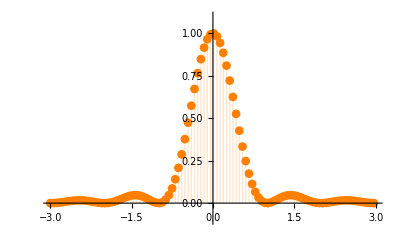
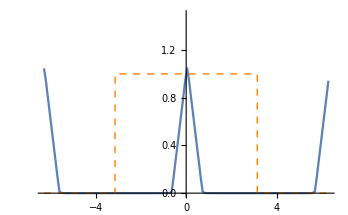

Abstract

GOAL OF THE PROJECT: Based on the famous book “Signals and Systems” 2nd Ed. and co-authored by Pr. Alan V. Oppenheim and  Pr. Alan S. Willsky, the aim of this project is to start a new updated edition of it that includes an online ebook version with animated and dynamic illustrations using the Wolfram platform.

SUMMARY OF WORK: The main objective is to update and convert all included figures and concepts, to animated and living figures and demonstrations, which dynamically can be changes by the professor or the students. This for sure will be a huge improvement and achievement in the new edition, and will definitely attract more students and professors too, to adopt this high-tech new edition book.

RESULTS AND FUTURE  WORK: Some large sections were converted including new animated illustrations, in addition to a sample slideshow which will be used next year on my teaching. This work was presented to Pr. Oppenheim and was impressed by the technology and even ask to get access to them online. Future work includes the development of more animations on signal processing mainly, and even start our own book on the subject using Wolfram technology.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

```mathematica
Nyquist-Shannon Sampling Theorem
```

```mathematica
The Nyquist-Shannon Sampling theorem is a fundamental one providing the condition on the sampling frequency of a band-width limited continuous-time signal in order to be able to reconstruct it perfectly from its discrete-time (sampled) version. It stated that the sampling frequency must be at least two times the highest frequency of the continuous-time signal spectrum.
```

## What is a Signal?

A signal is a time/space varying function which includes some useful information. Most of signals are continuous-time ones and hence can not be either stored (or transmitted) over realistic limited data storage (or band-limited propagation space) due to infinity of points to be processed.

#### Example of a continuous-time* signal - Mean Temperature during 2016 in Rabat, Morocco:

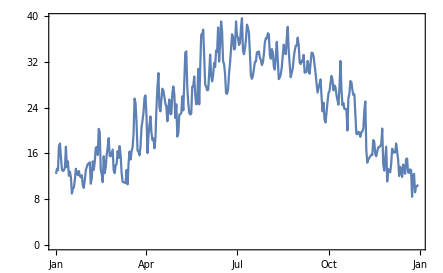

```mathematica
weatherData=WeatherData[{33.9716,6.8498}, "MeanTemperature", {{2016, 1, 1}, {2016, 12, 31}, "Day"}];
DateListPlot[weatherData,Joined -> True]
```

## Sampling Theorem

In order, to process real life signals either to store or transmit, we need to a sampling process them, making them discrete-time signal.

“A continuous-time signal x(t) can be sampled at a frequency f_s in order to get a discrete-time copy of it x[n], and afterwards be reconstructed perfectly to its original form x(t) if f_s>2 f_max with f_max is the maximum frequency value of the x(t) signal spectrum”

#### Plot of the signal x(t)=Sinc^2(t)

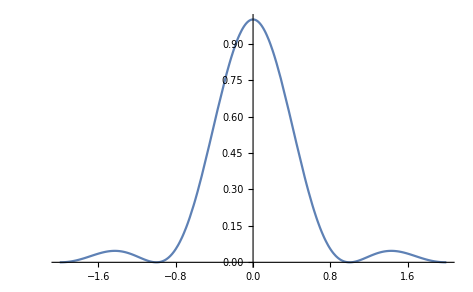

```mathematica
x[t_]:=(Sinc[Pi*t])^2;
Plot[x[t],{t,-2,2}]
```

## Sampling Process - Time Domain Analysis

Consider the function x(t)=Sinc^2(t) which represent a continuous-time signal.

#### Plot of the signal x(t)=Sinc^2(t):

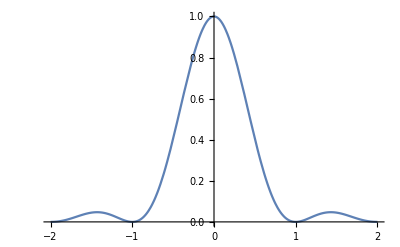

```mathematica
x[t_]:=(Sinc[Pi*t])^2;
Plot[x[t],{t,-2,2}]
```

## Sampling Process - Time Domain Analysis

Consider a sampling frequency f_sand let see what happen for different values of f_s.

#### Plot of the continuous - time and discrete - time (sampled) signals :

```mathematica
Manipulate[
Show[DiscretePlot[x[t],{t, -3, 3,1/fs},PlotRange->{{-3,3},{-0.1,1.1}},PerformanceGoal->"Quality",PlotStyle->Directive[Orange,Thick],PlotMarkers->Automatic],Plot[x[t],{t,-3,3}]],{{fs,15.25,"Frequency f_s"}, 0.5, 30,Appearance->"Labeled"},SaveDefinitions->True]
```

## Sampling Process - Frequency Domain

The spectrum analysis of signal x(t) allows us to understand easily and even prove the theorem ourselves.

TF[Sinc^2(a t)] = 1/(|a|)tri(f/a)

#### Fourier Transform of the signal x(t):

```mathematica
Simplify[FourierTransform[x[t],t,ω]]
```

(-2 ω Sign[ω]+(-2 π+ω) Sign[-2 π+ω]+(2 π+ω) Sign[2 π+ω])/(4 √2 π^(3/2))

#### Spectrum of the signal x(t):

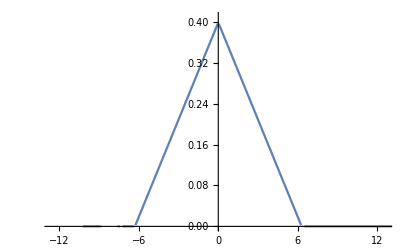

```mathematica
Plot[FourierTransform[x[t],t,ω],{ω,-10*2 Pi,10*2Pi},PlotRange->{{-2*2Pi,2*2Pi},{0,0.41}}]
```

## Sampling Process

Sampled signal x[n] (left) and its Fourier transform spectrum:

```mathematica
Manipulate[Row[{DiscretePlot[x[t],{t, -3, 3,1/fs},PlotRange->{{-3,3},{-0.1,1.1}},PerformanceGoal->"Quality",PlotStyle->Directive[Orange,Thick],PlotMarkers->Automatic,ImageSize->340],ListLinePlot[Join@@Table[Abs[Fourier[Table[N[x[n/fs]],{n,-4*fs,4*fs+1}]]],4],DataRange->{-4Pi,4Pi},PlotRange->{{-4Pi,4Pi},{0,1.5}},ImageSize->300]}],{{fs,15.25,"Frequency f_s"}, 0.5, 20,Appearance->"Labeled"}]
```

There will be overlapping of the spectrum, which we call an aliasing effect

## Reconstruction Process

The reconstruction process consists in the generation of the original continuous-time signal x(t) from the sampled version x[n]. As long as there is no aliasing effect, a simple low passband filter is enough to retrieve the original signal

#### Filtering the Spectrum of the sampled signal x[n] :

```mathematica
Manipulate[Show[ListLinePlot[Join@@Table[Abs[Fourier[Table[N[x[n/fs]],{n,-4*fs,4*fs}]]],2],DataRange->{-2Pi,2Pi},PlotRange->{{-2Pi,2Pi},{0,1.5}},ImageSize->300],Plot[HeavisidePi[x/(2*Pi)],{x,-2Pi,2Pi},Exclusions->None,PlotStyle->Directive[Orange,Thick,Dashed] ]],{{fs,8,"Frequency f_s"}, 0.5, 20,Appearance->"Labeled"}]
```

## Reconstruction Process

Depending on the existence of aliasing or not, the retrieved continuous-time signal could the perfect copy of the original or a distorted one.

#### Spectrum of the sample signal and the reconstructed version of the signal x[n] :

```mathematica
Manipulate[Row[{Show[ListLinePlot[Join@@Table[Abs[Fourier[Table[N[x[n/fs]],{n,-4fs,4fs}]]],2],PerformanceGoal->"Quality",DataRange->{-2Pi,2Pi},PlotRange->{{-2Pi,2Pi},{0,1.5}},ImageSize->300],Plot[HeavisidePi[x/(2*Pi)],{x,-2Pi,2Pi},Exclusions->None,PlotStyle->Directive[Orange,Thick,Dashed] ]],
ListLinePlot[Re[InverseFourier[Fourier[Table[N[x[n/fs]],{n,-4fs,4fs}]]]],DataRange->{-3,3},PlotRange->{{-3,3},{0,1.1}},ImageSize->300,PerformanceGoal->"Quality"] }],{{fs,8,"Frequency f_s"}, 0.5, 20,Appearance->"Labeled"}]
```

As long as the sampling frequency verifies the Nyquist - Shannon condition, we can reconstruct the original signal without distortion.

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

Code

Provide one of:

Link to the GitHub

Explicit code

Written Content / Lesson Plans

Conclusions in Detail

All Visualizations

Data Sources Links/References

Future Directions

Background Info Links/References

Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```